```mathematica
For[iteration=1,iteration <=3,iteration++,
skip={10,20,40}[[iteration]];
du=dv={1/50,1/100,1/200}[[iteration]];
massReduct=1/1000;
v1= 0;
m0=1;
Q0=8/10;
SourcesRParam = 1;
SourcesRParamR = 1;
SourcesSParam = 1;
SourcesSParamR =1;
SourcesS5Param = 0;
deltaUV5Param = 70;
QuvFactor =1;
Qreduct=Q0/m0*massReduct;
deltav =900;
v2 =v1+deltav;
RStarConst =-30;
Vvec = Table[v,{v,v1,v2,dv}];
MFunc = (m0^3-(v-v1)*massReduct)^(1/3);
QFunc = MFunc * Q0;
Clear[pdesolskip,RTable,STable,RvTable,RvvTable,RuTable,RuuTable,SvTable,SvvTable,SuTable,SuuTable];
Uvec = 2*RStarConst- Vvec;
Uvec0=Table[u,{u,Uvec[[-1]],Uvec[[1]],du}];
UvecSkipped = Uvec0[[1;;-1;;skip]];
VvecSkipped = Vvec[[1;;-1;;skip]];
deltaUV5 = (Uvec0[[1]]+Vvec[[1]])/2+deltaUV5Param; 
vsol=DSolve[{H'[v]==κp/.{Q->QFunc,m->MFunc},H[0]==0},H[v],{v,v1,v2}(*,Method->"StiffnessSwitching",WorkingPrecision->60*)];
vtilde=(H[v]/.vsol/.{v->Vvec})[[1]];
usol=DSolve[{H'[u]==κp/.{Q->(QFunc/.v->-u),m->(MFunc/.v->-u)},H[0]==0},H[u],u(*,{u,Uvec[[1]],Uvec[[-1]]},Method->"StiffnessSwitching",WorkingPrecision->60*)];
utilde=(H[u]/.usol/.{u->Uvec})[[1]];
Ttilde=(utilde+vtilde)/2;
MTable= MFunc/.{v->Vvec}//N100;
QTable = QFunc/.{v->Vvec}//N100;
QuvTable = QuvFactor *massReduct* MTable^-1 ;
QuvScale=MTable^-1;
MuTable = MFunc /. {v->-Uvec}//N100;
QuTable = QFunc /. {v->-Uvec}//N100;
κpu=(κp/.{m->μ,Q->Qu});
sInitFixed = Log[-r *f/2]+Log[κpu]-Log[κp];
DRDUFixed=r f *κpu/κp;
DLogκpuDu=D[Log[κpu],μ]*D[(MFunc/.v->-u),u]+D[Log[κpu],Qu]*D[(QFunc/.v->-u),u];
DSDUFixed=D[Log[-r f ],r] *DRDUFixed/(2r)+DLogκpuDu;
SourcesR=massReduct*SourcesRParam/MTable^3;
SourcesS = massReduct*SourcesSParam/MTable^5;
SourcesRR =massReduct* SourcesRParamR/MTable^4;
SourcesRS = massReduct*SourcesSParamR/MTable^6;
SourcesR5=0*Vvec;
SourcesS5 = massReduct*SourcesS5Param*MTable;
time0=AbsoluteTiming[
RStarVector=Table[ (Ttilde[[j]]/κp/.{m->MTable[[j]],Q->QTable[[j]]}),{j,1,Length[MTable]}];
rInit=Table[RFromRStar[RStarVector[[j]],MTable[[j]],QTable[[j]]],{j,1,Length[MTable]}];
RInitVector = Table[ rInit[[j]]^2,{j,1,Length[MTable]}];
SInitVector =  Table[ (sInitFixed/.{m->MTable[[j]],μ->MuTable[[j]],r->rInit[[j]],Q->QTable[[j]],Qu->QuTable[[j]]})//N,{j,1,Length[MTable]}];
DRInitVector =  Table[ (DRDUFixed/.{m->MTable[[j]],μ->MuTable[[j]],r->rInit[[j]],Q->QTable[[j]],Qu->QuTable[[j]]})//N,{j,1,Length[MTable]}];
DSInitVector =  Table[ (DSDUFixed/.{m->MTable[[j]],μ->MuTable[[j]],u->Uvec[[j]],r->rInit[[j]],Q->QTable[[j]],Qu->QuTable[[j]]})//N,{j,1,Length[MTable]}];
midpointDR = (DRInitVector[[2;;]]+DRInitVector[[;;-2]])/2;
midpointDS = (DSInitVector[[2;;]]+DSInitVector[[;;-2]])/2;
{Ruv,Suv}=ComputeRuvSuvQuvScale[RInitVector,SInitVector,(QTable[[2;;]]+QTable[[;;-2]])/2,SourcesR,SourcesS,QuvTable,Uvec0[[1]]+Vvec[[1]],QuvScale, dv,SourcesRR,SourcesRS,SourcesR5,SourcesS5,deltaUV5];
R2InitVector=RInitVector[[2;;]]+du*(midpointDR+1/2*dv*Ruv);
S2InitVector=SInitVector[[2;;]]+du*(midpointDS+1/2*dv*Suv);];
time2=AbsoluteTiming[pdesolskip=pyPdeSolveQuvScale[skip,R2InitVector,RInitVector,S2InitVector,SInitVector,(QTable//N),(du//N),(dv//N),SourcesR//N,SourcesS//N,QuvTable//N,(Uvec0[[1]]+Vvec[[1]])//N, QuvScale // N,SourcesRR//N,SourcesRS//N,SourcesR5 // N,SourcesS5//N,deltaUV5//N];];
(* R,S,Rv,Rvv,Ru,Ruu,Sv,Svv,Su,Suu *)
RTable = Normal[pdesolskip[[1]]];
STable = Normal[pdesolskip[[2]]];
RvTable = Normal[pdesolskip[[3]]];
RvvTable = Normal[pdesolskip[[4]]];
RuTable = Normal[pdesolskip[[5]]];
RuuTable = Normal[pdesolskip[[6]]];
SvTable = Normal[pdesolskip[[7]]];
SvvTable = Normal[pdesolskip[[8]]];
SuTable = Normal[pdesolskip[[9]]];
SuuTable = Normal[pdesolskip[[10]]];
cu = RuTable*SuTable-RuuTable;
cv = RvTable*SvTable-RvvTable;
cuv = cu-cv;
RTables[du] = RTable;
STables[du] = STable;
RvTables[du] = RvTable;
RvvTables[du] = RvvTable;
RuTables[du] = RuTable;
RuuTables[du] = RuuTable;
SvTables[du] = SvTable;
SvvTables[du] = SvvTable;
SuTables[du] = SuTable;
SuuTables[du] = SuuTable;
cus[du]=cu;
cvs[du]=cv;
]
```

10% Done

20% Done

30% Done

40% Done

50% Done

60% Done

70% Done

80% Done

90% Done

100% Done

Done calculating

10% Done

20% Done

30% Done

40% Done

50% Done

60% Done

70% Done

80% Done

90% Done

100% Done

Done calculating

10% Done

20% Done

30% Done

40% Done

50% Done

60% Done

70% Done

80% Done

90% Done

100% Done

Done calculating

```mathematica
TheImageSize=220;
```

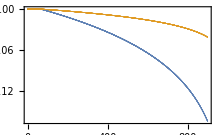

```mathematica
ExportAndShow["S error diff",ListPlot[{{VvecSkipped,STables[1/100][[;;,-1]]-STables[1/50][[;;,-1]]}//Transpose,{VvecSkipped,STables[1/200][[;;,-1]]-STables[1/100][[;;,-1]]}//Transpose},PlotRange->All,Frame->True,FrameLabel->{MaTeX@"v"},PlotLegends->MaTeX/@{"S\\left[du=\\frac{1}{50}\\right]-S\\left[du=\\frac{1}{100}\\right]","S\\left[du=\\frac{1}{100}\\right]-S\\left[du=\\frac{1}{200}\\right]"},ImageSize->TheImageSize]]
```

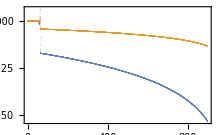

```mathematica
ExportAndShow["R error diff",ListPlot[{{VvecSkipped,RTables[1/100][[;;,-1]]-RTables[1/50][[;;,-1]]}//Transpose,{VvecSkipped,RTables[1/200][[;;,-1]]-RTables[1/100][[;;,-1]]}//Transpose},PlotRange->All,Frame->True,FrameLabel->{MaTeX@"v"},PlotLegends->MaTeX/@{"R\\left[du=\\frac{1}{50}\\right]-R\\left[du=\\frac{1}{100}\\right]","R\\left[du=\\frac{1}{100}\\right]-R\\left[du=\\frac{1}{200}\\right]"},ImageSize->TheImageSize]]
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

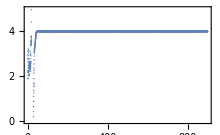

```mathematica
ExportAndShow["S error ratio",ListPlot[{{VvecSkipped,(STables[1/100][[;;,-1]]-STables[1/50][[;;,-1]])/(STables[1/200][[;;,-1]]-STables[1/100][[;;,-1]])}//Transpose},Frame->True,PlotRange->{{0,900},{0,5}},FrameLabel->{MaTeX@"v"},ImageSize->TheImageSize]]
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

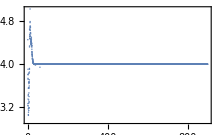

```mathematica
ExportAndShow["R error ratio",ListPlot[{{VvecSkipped,(RTables[1/100][[;;,-1]]-RTables[1/50][[;;,-1]])/(RTables[1/200][[;;,-1]]-RTables[1/100][[;;,-1]])}//Transpose},PlotRange->All,Frame->True,FrameLabel->{MaTeX@"v"},ImageSize->TheImageSize]]
```

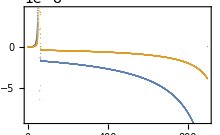

```mathematica
ExportAndShow["R,v error diff",ListPlot[{{VvecSkipped[[2;;]],RvTables[1/100][[2;;,-1]]-RvTables[1/50][[2;;,-1]]}//Transpose,{VvecSkipped[[2;;]],RvTables[1/200][[2;;,-1]]-RvTables[1/100][[2;;,-1]]}//Transpose},Frame->True,FrameLabel->{MaTeX@"v"},PlotLegends->MaTeX/@{"R_{,v}\\left[du=\\frac{1}{50}\\right]-R_{,v}\\left[du=\\frac{1}{100}\\right]","R_{,v}\\left[du=\\frac{1}{100}\\right]-R_{,v}\\left[du=\\frac{1}{200}\\right]"},ImageSize->TheImageSize]]
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

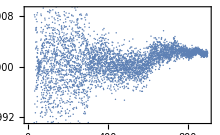

```mathematica
ExportAndShow["R,v error ratio",ListPlot[{{VvecSkipped[[2;;]],(RvTables[1/100][[2;;,-1]]-RvTables[1/50][[2;;,-1]])/(RvTables[1/200][[2;;,-1]]-RvTables[1/100][[2;;,-1]])}//Transpose},Frame->True,FrameLabel->{MaTeX@"v"},ImageSize->TheImageSize]]
```

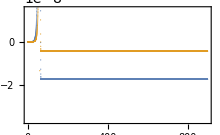

```mathematica
ExportAndShow["R,u error diff",ListPlot[{{VvecSkipped[[2;;]],RuTables[1/100][[2;;,-2]]-RuTables[1/50][[2;;,-2]]}//Transpose,{VvecSkipped[[2;;]],RuTables[1/200][[2;;,-2]]-RuTables[1/100][[2;;,-2]]}//Transpose},Frame->True,FrameLabel->{MaTeX@"v"},PlotLegends->MaTeX/@{"R_{,u}\\left[du=\\frac{1}{50}\\right]-R_{,u}\\left[du=\\frac{1}{100}\\right]","R_{,u}\\left[du=\\frac{1}{100}\\right]-R_{,u}\\left[du=\\frac{1}{200}\\right]"},ImageSize->TheImageSize]]
```

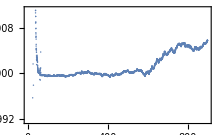

```mathematica
ExportAndShow["R,u error ratio",ListPlot[{{VvecSkipped[[2;;]],(RuTables[1/100][[2;;,-2]]-RuTables[1/50][[2;;,-2]])/(RuTables[1/200][[2;;,-2]]-RuTables[1/100][[2;;,-2]])}//Transpose},Frame->True,FrameLabel->{MaTeX@"v"},ImageSize->TheImageSize]]
```

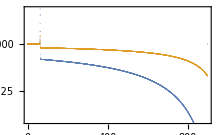

```mathematica
ExportAndShow["S,v error diff",ListPlot[{{VvecSkipped[[2;;]],SvTables[1/100][[2;;,-1]]-SvTables[1/50][[2;;,-1]]}//Transpose,{VvecSkipped[[2;;]],SvTables[1/200][[2;;,-1]]-SvTables[1/100][[2;;,-1]]}//Transpose},Frame->True,FrameLabel->{MaTeX@"v"},PlotLegends->MaTeX/@{"S_{,v}\\left[du=\\frac{1}{50}\\right]-S_{,v}\\left[du=\\frac{1}{100}\\right]","S_{,v}\\left[du=\\frac{1}{100}\\right]-S_{,v}\\left[du=\\frac{1}{200}\\right]"},ImageSize->TheImageSize]]
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

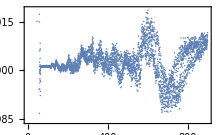

```mathematica
ExportAndShow["S,v error ratio",ListPlot[{{VvecSkipped[[2;;]],(SvTables[1/100][[2;;,-2]]-SvTables[1/50][[2;;,-2]])/(SvTables[1/200][[2;;,-2]]-SvTables[1/100][[2;;,-2]])}//Transpose},Frame->True,FrameLabel->{MaTeX@"v"},ImageSize->TheImageSize]]
```

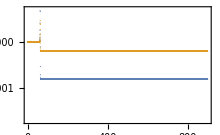

```mathematica
ExportAndShow["S,u error diff",ListPlot[{{VvecSkipped[[2;;]],SuTables[1/100][[2;;,-2]]-SuTables[1/50][[2;;,-2]]}//Transpose,{VvecSkipped[[2;;]],SuTables[1/200][[2;;,-2]]-SuTables[1/100][[2;;,-2]]}//Transpose},Frame->True,FrameLabel->{MaTeX@"v"},PlotLegends->MaTeX/@{"S_{,u}\\left[du=\\frac{1}{50}\\right]-S_{,u}\\left[du=\\frac{1}{100}\\right]","S_{,u}\\left[du=\\frac{1}{100}\\right]-S_{,u}\\left[du=\\frac{1}{200}\\right]"},ImageSize->TheImageSize]]
```

Power::infy: Infinite expression 1/0. encountered.

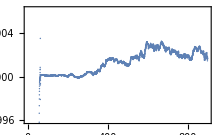

```mathematica
ExportAndShow["S,u error ratio",ListPlot[{{VvecSkipped[[2;;]],(SuTables[1/100][[2;;,-2]]-SuTables[1/50][[2;;,-2]])/(SuTables[1/200][[2;;,-2]]-SuTables[1/100][[2;;,-2]])}//Transpose},Frame->True,FrameLabel->{MaTeX@"v"},ImageSize->TheImageSize]]
```